## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

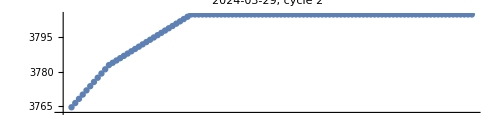
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

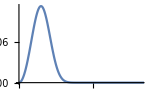
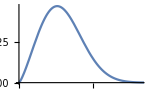
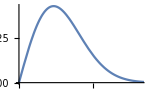
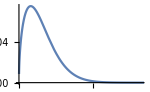

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

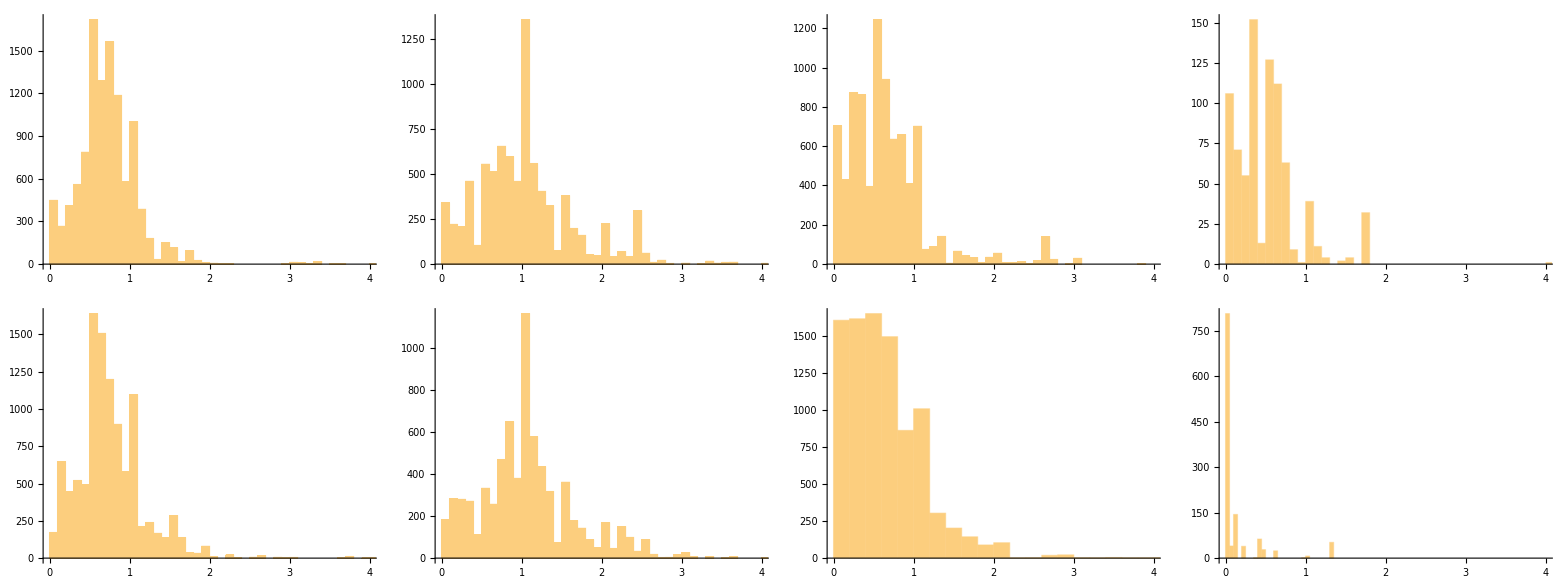

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```